# Rb87 Calculations

## Physical Constants

```mathematica
e = 1.6*10^-19; (*[C]*)
c = 3*10^8; (*[m/s]*)
a0 = 5.29*10^-11;(*[m]*)
μ0 = 4 π * 10^-7; (*[N/A^2,T·m/A]*)
ϵ0 = 8.85*10^-12;(*[A^2 s^4/m^3kg]*)
μB = (e ℏ)/(2 me);(*[J/T]*)
ℏ= 1.05*10^-34;(*[J·s]*)
h=2 π ℏ;
EHartree = 2*(13.6);(*[eV]*)
me = 9.11*10^-31;(*[kg]*)
mp = 1.67*10^-27;(*[kg]*)
eVperJ = 1/(1.6*10^-19);(*[eV/J]*)
α=1/137;
```

## Rb87 Constants

Default units are SI, except frequencies which for now are GHz.

```mathematica
INuc = 3/2;(* nuclear spin *)
mRb = 1.4192261*10^-25; (*[kg]*)
gS = 2.00023; (*Lande g, spin*)
gL = 1 ; (*This might be specifically for L=0*)
gI = -0.000995;
D2MatElem = 3.584*10^-29;(*<J=1/2||er||J'=3/2>[C*m]*)
D1MatElem = 2.537*10^-29;(*<J=1/2||er||J'=1/2>[C*m]*)
λD1 = 794.97885098*10^-9;(*[m]*) 
λD2 = 780.24120968613*10^-9;(*[m]*)
νD1 = 384.230484468562; (*[THz]*)
νD2 = 377.10746354 ;(*[THz]*)
νHF = 6.83468261090429 ;(*[Ghz]*)
ΓD2 = 2π 6.0659*10^6 ;(*[rad Hz]*)
```

```mathematica
EHF = h 10^9 νHF;(*[J]*)
EHFeV = JToeV[EHF]; (*duh*)
```

## Misc. Functions

Conversion functions, for explicitly followable unit changes in the code, at the risk of handicapping myself later.

```mathematica
GHzToJ[ν_]:=10^9 h ν;
GHzToeV[ν_]:=(10^9 h ν)/e 
JToGHz[u_]:=u/(10^9 h);
JToeV[u_]:=u/e;
eVToGHz[u_]:=e/(10^9 h)u;
```

```mathematica
NormalRandoms[x0_,σ_,n_,dx_]:=
Module[{x,y,pts,dist},
dist[x_]:=PDF[NormalDistribution[x0,σ],x];
pts =ConstantArray[0,n];
For[i=1,i<n+1,i++,
	x = dx*RandomReal-x0;
	y = 1/(√(2 π))RandomReal;
	While[pts[[i]]==0,
		If[y<dist[x],pts[[i]]= x,pts[[i]]=0];
	]
	]
pts
]
```

## Zeeman shifts

### Ground state hyperfine level shifts

This calculation seems only first order, and doesn’t seem to actually be diagonalizing the Hamiltonian in general. Why this not do like Python??

```mathematica
Clear[J,L,F,FF,mF,mFF]
```

```mathematica
HFZeemanMatElem[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},q_,Bz_]:=KroneckerDelta[mF,mFF]μB Bz (ClebschGordan[{F,mF},{1,q},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]));
```

```mathematica
S = 1/2; L = 0; J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-I(I+1))
+gI(F(F+1)-J(J+1)+I(I+1)))/(2F(F+1));
```

```mathematica
States = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{2,1}}],1]
```

{{2,-2},{2,-1},{2,0},{2,1},{2,2},{1,-1},{1,0},{1,1}}

Compute Hamiltonians in eV to avoid ridiculously small numbers

```mathematica
q=0; dim = Length[States];
HZ1[Bz_]=Table[Table[JToeV[HFZeemanMatElem[INuc,J,gJ,States[[i]],States[[j]],q,Bz]],{i,1,dim}],{j,1,dim}];
```

ClebschGordan::phy: ThreeJSymbol[{2,-1},{1,0},{2,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,0},{1,0},{2,2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,1},{1,0},{2,2}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
HAtom = EHFeV{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
HTotal[B_]=HAtom + HZ1[B];
ZShifts[B_]=Eigenvalues[HTotal[B]];(*Eigenenergies [eV]*)
```

```mathematica
BList = Range[0,0.5,.1];
ZShiftsData = Range[0,Length[ShiftsMat]];
ZShiftsMat = Transpose@Table[ZShifts[B],{B,BList}];
For[i = 0, i< Length[ZShiftsMat],i++,
	ZShiftsData[[i]] = Transpose@{BList,Sort[[ZShiftsMat[[i]]]]}
]
```

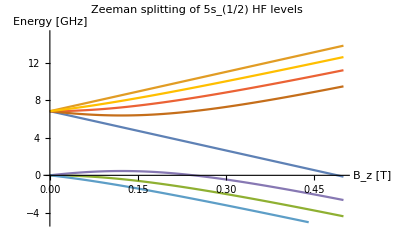

```mathematica
Plot[Evaluate[eVToGHz[Sort[ZShifts[B],Greater]]],{B,0,.5},PlotRange->{{0,0.5},{-5,15}},PlotLabel->"Zeeman splitting of 5s_(1/2) HF levels ",AxesLabel->{"B_z [T]","Energy [GHz]"}]
```

### Differential Hyperfine Shifts

m=0,m’=0 has a quadratic shift

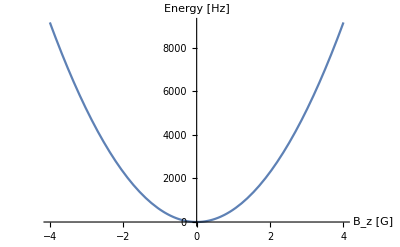

```mathematica
Plot[eVToGHz[ZShifts[10^-4 B][[4]]-EHFeV-ZShifts[10^-4 B][[3]]]/10^-9,{B,-4,4},PlotLabel->"",AxesLabel->{"B_z [G]","Energy [Hz]"}]
```

F=2,m=0,F=1,m=1

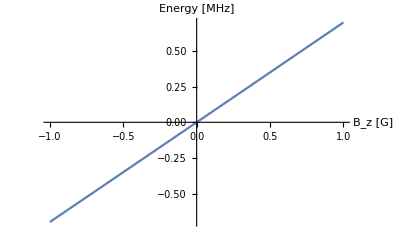

```mathematica
Plot[eVToGHz[ZShifts[10^-4 B][[4]]-EHFeV-ZShifts[10^-4 B][[7]]]/10^-3,{B,-1,1},PlotLabel->"",AxesLabel->{"B_z [G]","Energy [MHz]"}]
```

For a given Bz, the scalar Zeeman shifts are as a function of some field in the cylindrical radial direction ρ. The plot below shows the frequency offset (from the degenerate hyperfine resonance) needed to drive  F=2,m=0,F=1,m=1.

```mathematica
Manipulate[Plot[eVToGHz[ZShifts[10^-4 √(Bz^2+Bρ^2)][[4]]-EHFeV-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3,{Bρ,-.4,.4},PlotRange->{1.2,1.5},AxesLabel->{"B_ρ [G]","Energy [MHz]"},PlotLabel->"f_offset 2,0->1,1 from degenerate HF resonance"],{Bz,0,3.8}]
```

Deduce Bρ given two resonances for F=2,m=0 to F=1,m=1 measured for two different Bz. Bz coils were first set to some value Bz, and resonance at f_offset = 2.7144 MHz, then to Bz/2, with f_offset = 1.3697 MHz.

```mathematica
F2m0ToF1m1Offset[Bz_,Bρ_]:=eVToGHz[ZShifts[10^-4 √(Bz^2+Bρ^2)][[4]]-EHFeV-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3
```

```mathematica
eVToGHz[-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3//FullSimplify
```

-3417.34+0.00139064 √(Bz^2+Bρ^2)+0.403213 √(7.18304×10^7+12.0295 Bz^2+12.0295 Bρ^2+29395.3 √(Bz^2+Bρ^2))

```mathematica
Solve[-3417.3413054521443+0.0013906403370048004 √(BzSq+Bρ^2)+0.40321259623427075 √(7.183044056176053*^7+12.029488171690414 BzSq+12.029488171690414 Bρ^2+29395.296139093578 √(BzSq+Bρ^2))==2.7144,BzSq]
```

{{BzSq→8.00332×10^-93 (1.87098×10^93-1.24948×10^92 Bρ^2)},{BzSq→8.00332×10^-93 (7.51434×10^98-1.24948×10^92 Bρ^2)}}

```mathematica
8.003317964971477*^-93 (1.8709769115158673*^93-1.2494817829014793*^92 Bρ^2)//FullSimplify
```

14.974-1. Bρ^2

```mathematica
8.003317964971477*^-93 (7.514341258322977*^98-1.2494817829014793*^92 Bρ^2)//FullSimplify
```

6.01397×10^6-1. Bρ^2

```mathematica
Solve[-3417.3413054521443+0.0013906403370048004 √(BzSq/4+Bρ^2)+0.40321259623427075 √(7.183044056176053*^7+12.029488171690414 BzSq/4+12.029488171690414 Bρ^2+29395.296139093578 √(BzSq/4+Bρ^2))==1.3697,BzSq]
```

{{BzSq→7.39183×10^-88 (2.06566×10^88-5.41138×10^87 Bρ^2)},{BzSq→7.39183×10^-88 (3.2493×10^94-5.41138×10^87 Bρ^2)}}

```mathematica
7.39182789838621*^-88 (2.065658553912506*^88-5.411381399820311*^87 Bρ^2)//FullSimplify
```

15.269-4. Bρ^2

```mathematica
Solve[14.974023127981791-1. Bρ^2==15.268992527350578-4. Bρ^2,Bρ](*Bρ [G]*)
```

{{Bρ→-0.313565},{Bρ→0.313565}}

## Optical Trapping

### Optical Molasses

```mathematica
Is = g1/g2(ℏ γD2 ωD2^3)/(12 π c^2) ;g1 = 5; g2 = 7;(*saturation intensity. gi = ith state degeneracy*)
```

```mathematica
β[Δ_,I_]:=8ℏ kD2^2(-Δ/γD2)/((1+4 Δ^2/γD2^2)^2)I/Is;(*s set to 1*)
F[Δ_,I_]:= (ℏ kD2 γD2)/2 I/Is 1/(1+(4 Δ^2)/γD2^2+I/Is);
```

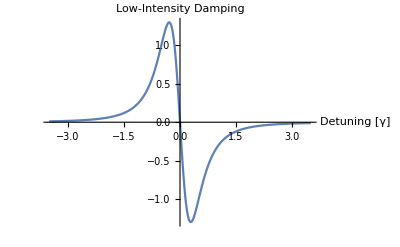

```mathematica
Plot[β[Δ*γD2,Is]/(ℏ kD2^2),{Δ,-3.5,3.5},PlotRange-> Full,AxesLabel->{"Detuning [γ]","Low-Intensity Damping"}]
```

Cool atoms into optical molasses.
Program:
	- Generate array of atoms with gaussian velocity dist O(1 m/s),
	a random initial state either e or g,F where F=2,1 are the 
	hyperfine levels.
	- For[t = 0, t < t_exp, t+=dt,
		For[i = 0, i< # of atoms, i++,
			x = v*t + .5 (F[v]/m) t^2
			if RandomReal > decays/dt  // not quite
				state = |g,F = Random[1 or 2] >	
		]
		If i mod int(t_exp/shots)
			ListPlot[Transpose@{atom_positions,atom_velocities}]
	  ]

```mathematica
pts = NormalRandoms[0,2,10,10]
```

$Aborted

#### Sensitivity to beam imbalance

An atom in our FORT during RO is exposed to the MOT light for ~ (1-.53)*8*10^-7 s

```mathematica
d=.53
```

0.53

```mathematica
tFree =(1-d)*8*10^-7;
fChop= 1.25*10^6;
tRO = 2*10^-3;(*5*10^-3;*)
tTotal= tFree*fChop*tRO
```

0.00094

MOT intensity per arm:

```mathematica
IMOT = (5*10^-4)/(π (.005)^2) ;(*Assumes 1mm wide circular beams, ~.5mW*)
```

Consider two beams of a MOT with differing intensities.

```mathematica
FNet[I1_,I2_] := F[-3 γD2,I1]-F[-3 γD2,I2];
```

```mathematica
Clear[t]
```

```mathematica
Manipulate[Plot[(1/2 FNet[α s,.9 α*s]/mRb ((1-duty)*8*10^-7)^2)/10^-6,{α,.1,1},AxesLabel->{"I_Rel","Distance traveled"}],{duty,.3,.8}]
```

### Magneto-Optical Trap

### Far Off Resonance Trap (FORT)

An atom has some temperature T, in a trap of radius w0. What is the shortest time it will take the atom to move outside of the beam cross-section (perpendicular to the optical axis) if the beam is turned off instantaneously?

```mathematica
vRMS[T_]:= √((2 kB T)/mRb);  w0 = 2.5*10^-6;
```

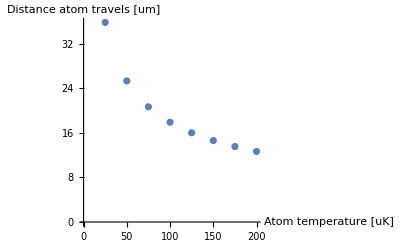

```mathematica
ListPlot[Table[{T/10^-6,w0/(vRMS[T]*10^-6)},{T,Range[25*10^-6,200*10^-6,25*10^-6]}],AxesLabel-> {"Atom temperature [uK]","Distance atom travels [um]"}]
```

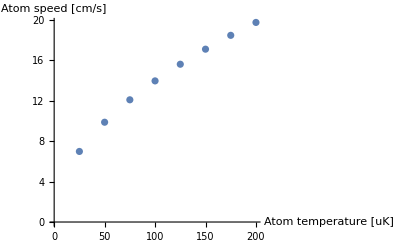

```mathematica
ListPlot[Table[{T/10^-6,vRMS[T]*100},{T,Range[25*10^-6,200*10^-6,25*10^-6]}],AxesLabel-> {"Atom temperature [uK]","Atom speed [cm/s]"}]
```